```mathematica
f[u_,uh_,z_,θ_,μ_]:=1-(u/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ)u^(2z-2θ+2)/uh^(2z-2θ)(1-(u/uh)^(θ-z))
```

```mathematica
qcrit[us_,uh_,z_,θ_,μ_]:=us^(θ/2-z)Sqrt[f[us,uh,z,θ,μ]]/μ/(1-(us/uh)^(z-θ));
μext[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/(z-θ)/uh;
```

```mathematica
ut[us_,uh_,z_,θ_,μ_,q_]:=NDSolveValue[{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+1/(2 uh^2 (2-θ))u[t]^3 (-2 (-2+θ) (-2-z+θ) u[t]^(-2 z) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(-2 θ) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(-2 θ) (1-(u[t]/uh)^(-z+θ)))+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^3 (-2 (-2+θ) (-2-z+θ) u[t]^(-2 z) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(-2 θ) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(-2 θ) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]==us,u'[0]==0},u,{t,0.01,5},Method->"BDF"];
ut1[t1_,us_,uh_,z_,θ_,μ_,q_]:=ut[us,uh,z,θ,μ,q][t1];
ut[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]][0.5]
ut1[0.5,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]
```

0.685807

0.685807

```mathematica
dfu[t1_,us_,uh_,z_,θ_,μ_,q_]:=D[ut[us,uh,z,θ,μ,q][t],t]/.{t->t1};
pu[t1_,us_,uh_,z_,θ_,μ_,q_]:=ut1[t1,us,uh,z,θ,μ,q]^(θ/2-1)dfu[t1,us,uh,z,θ,μ,q]/Sqrt[ut1[t1,us,uh,z,θ,μ,q]^(2-2z)f[ut1[t1,us,uh,z,θ,μ,q],uh,z,θ,μ]^3-dfu[t1,us,uh,z,θ,μ,q]^2f[ut1[t1,us,uh,z,θ,μ,q],uh,z,θ,μ]];
βpu[t1_,us_,uh_,z_,θ_,μ_,q_]:=pu[t1,us,uh,z,θ,μ,q]/((ut1[t1,us,uh,z,θ,μ,q]*(ut1[t1,us,uh,z,θ,μ,q]/uh)^(z-θ)*(-2-z+θ))/uh^2+(ut1[t1,us,uh,z,θ,μ,q]^(1+2*z-2*θ)*uh^(-2*z+2*θ)*(-z+θ)*(2*(ut1[t1,us,uh,z,θ,μ,q]/uh)^z*(1+z-θ)+(ut1[t1,us,uh,z,θ,μ,q]/uh)^θ*(-2-z+θ))*μ^2)/(2*(ut1[t1,us,uh,z,θ,μ,q]/uh)^z*(-2+θ)));
```

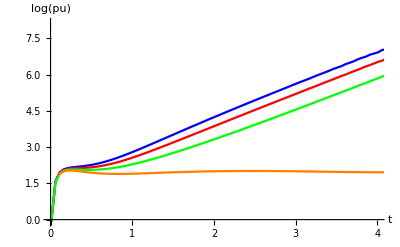

```mathematica
Show[
ListLinePlot[Table[{i,pu[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],0.500qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,pu[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],0.670qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,pu[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],0.830qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,pu[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],0.996qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Orange],AxesOrigin->{0,0},AxesLabel->{t,Log[pu]},PlotRange->{{0,4},All}
]
```

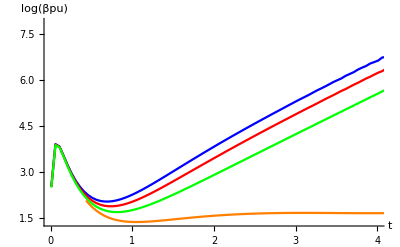

```mathematica
Show[
ListLinePlot[Table[{i,βpu[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],0.500qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],0.670qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],0.830qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],0.996qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Orange],AxesOrigin->{0,0},AxesLabel->{t,Log[βpu]},PlotRange->{{0,4},All}
]
```

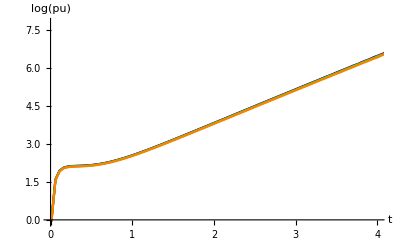

```mathematica
Show[
ListLinePlot[Table[{i,pu[i,0.1,1,1.01,0.000,0.75μext[1,1.01,0.000],0.7qcrit[0.1,1,1.01,0.000,0.75μext[1,1.01,0.000]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,pu[i,0.1,1,1.01,0.005,0.75μext[1,1.01,0.005],0.7qcrit[0.1,1,1.01,0.005,0.75μext[1,1.01,0.005]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,pu[i,0.1,1,1.01,0.010,0.75μext[1,1.01,0.010],0.7qcrit[0.1,1,1.01,0.010,0.75μext[1,1.01,0.010]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,pu[i,0.1,1,1.01,0.020,0.75μext[1,1.01,0.020],0.7qcrit[0.1,1,1.01,0.020,0.75μext[1,1.01,0.020]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Orange],AxesOrigin->{0,0},AxesLabel->{t,Log[pu]},PlotRange->{{0,4},All}
]
```

NDSolveValue::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

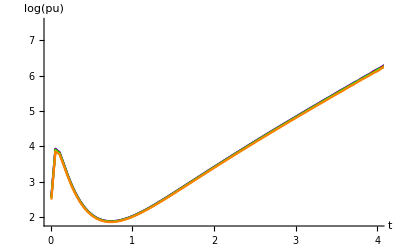

```mathematica
Show[
ListLinePlot[Table[{i,βpu[i,0.1,1,1.01,0.000,0.75μext[1,1.01,0.000],0.7qcrit[0.1,1,1.01,0.000,0.75μext[1,1.01,0.000]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.01,0.005,0.75μext[1,1.01,0.005],0.7qcrit[0.1,1,1.01,0.005,0.75μext[1,1.01,0.005]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.01,0.010,0.75μext[1,1.01,0.010],0.7qcrit[0.1,1,1.01,0.010,0.75μext[1,1.01,0.010]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.01,0.020,0.75μext[1,1.01,0.020],0.7qcrit[0.1,1,1.01,0.020,0.75μext[1,1.01,0.020]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Orange],AxesOrigin->{0,0},AxesLabel->{t,Log[pu]},PlotRange->{{0,4},All}
]
```

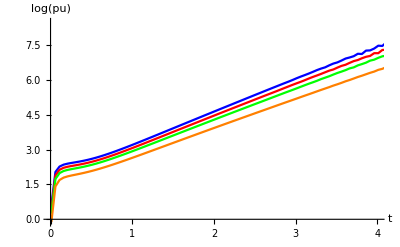

```mathematica
Show[
ListLinePlot[Table[{i,pu[i,0.1,1,1.2,0.00,0.75μext[1,1.2,0.00],0.7qcrit[0.1,1,1.2,0.00,0.75μext[1,1.2,0.00]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,pu[i,0.1,1,1.2,0.10,0.75μext[1,1.2,0.10],0.7qcrit[0.1,1,1.2,0.10,0.75μext[1,1.2,0.10]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,pu[i,0.1,1,1.2,0.20,0.75μext[1,1.2,0.20],0.7qcrit[0.1,1,1.2,0.20,0.75μext[1,1.2,0.20]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,pu[i,0.1,1,1.2,0.40,0.75μext[1,1.2,0.40],0.7qcrit[0.1,1,1.2,0.40,0.75μext[1,1.2,0.40]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Orange],AxesOrigin->{0,0},AxesLabel->{t,Log[pu]},PlotRange->{{0,4},All}
]
```

NDSolveValue::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

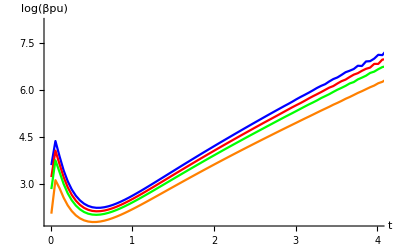

```mathematica
Show[
ListLinePlot[Table[{i,βpu[i,0.1,1,1.2,0.00,0.75μext[1,1.2,0.00],0.7qcrit[0.1,1,1.2,0.00,0.75μext[1,1.2,0.00]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.2,0.10,0.75μext[1,1.2,0.10],0.7qcrit[0.1,1,1.2,0.10,0.75μext[1,1.2,0.10]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.2,0.20,0.75μext[1,1.2,0.20],0.7qcrit[0.1,1,1.2,0.20,0.75μext[1,1.2,0.20]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.2,0.40,0.75μext[1,1.2,0.40],0.7qcrit[0.1,1,1.2,0.40,0.75μext[1,1.2,0.40]]]//Abs//Log},{i,0.01,5,0.05}],PlotStyle->Orange],AxesOrigin->{0,0},AxesLabel->{t,Log[βpu]},PlotRange->{{0,4},All}
]
```